```mathematica
ClearAll["Global`*"];
```

```mathematica
f[x_]=√x-2*Cos[x];
```

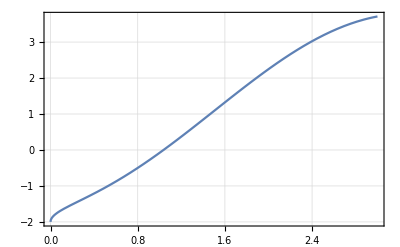

```mathematica
Plot[√x-2*Cos[x],{x,0,3}, Frame->True,GridLines->Automatic]
```

```mathematica
(*Метод секущих*)
```

```mathematica
Secuch[a_, b_]:=(
x[0]=a;
x[1]=b;
n=0;
eps=0.001;
ep=1;
Print["Начало: ", a, "; Конец: ", b];
Print["n= ", n, " x= ", x[n], " f[x]= ", N[f[x[n]]], " dx= ", ep];
n++;
Print["n= ", n, " x= ", x[n], " f[x]= ", N[f[x[n]]], " dx= ", ep];
While[ep > eps, x[n+1] = x[n]-N[f[x[n]]*(x[n]-x[n-1])/(f[x[n]]-f[x[n-1]])];
ep=Abs[x[n+1]-x[n]];
n++;Print["n= ", n, " x= ", x[n], " f[x]= ", N[f[x[n]]], " dx= ", ep]];
);
```

```mathematica
Secuch[0, 3]
```

Начало: 0; Конец: 3

n= 0 x= 0 f[x]= -2. dx= 1

n= 1 x= 3 f[x]= 3.71204 dx= 1

n= 2 x= 1.05041 f[x]= 0.0304724 dx= 1.94959

n= 3 x= 1.03428 f[x]= -0.00530124 dx= 0.0161368

n= 4 x= 1.03667 f[x]= -0.0000127547 dx= 0.00239129

n= 5 x= 1.03667 f[x]= 5.40828×10^-9 dx= 5.76727×10^-6

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Комбинированный метод*)
```

```mathematica
f[x_]=√x-2*Cos[x];
```

```mathematica
f1[x_]=Dt[f[x],x]
```

1/(2 √x)+2 Sin[x]

```mathematica
f2[x_]=Dt[f[x],{x,2}]
```

-1/(4 x^(3/2))+2 Cos[x]

```mathematica
N[f2[1]*f[1]]
```

-0.0669506

```mathematica
z0=0;
z1=3;
x=1;
n=0;
eps=0.001;
ep=1;
Print["n = ", n, " x = ", x, " z1 = ", z1, " delX = ", ep];
While[ep>eps,z1=N[z1-f[z1]*(z0-z1)/(f[z0]-f[z1])];x=N[x-f[x]/f1[x]];ep=Abs[z1-x];z0=x;n++;
Print["n = ", n, " x = ", x, " z1 = ", z1, " delX = ", ep]];
```

n = 0 x = 1 z1 = 3 delX = 1

n = 1 x = 1.03692 z1 = 1.05041 delX = 0.0134888

n = 2 x = 1.03667 z1 = 1.03667 delX = 5.91033×10^-7